## Input

```mathematica
A=ReadList[FileNameJoin[{NotebookDirectory[],"\\original_actions.txt"}]]⟦1⟧;
B=ReadList[FileNameJoin[{NotebookDirectory[],"\\new_actions.txt"}]]⟦1⟧;
(* A=Tally[A,#1⟦1⟧==#2⟦1⟧&]⟦All,1⟧ *)
```

## Data Processing

```mathematica
ShowData[A_]:=(DT=Table[A⟦i,1⟧-A⟦i-1,1⟧,{i,2,Length[A]}];
VXT=Table[(A⟦i,2⟧-A⟦i-1,2⟧)/(A⟦i,1⟧-A⟦i-1,1⟧),{i,2,Length[A]}];
VYT=Table[(A⟦i,3⟧-A⟦i-1,3⟧)/(A⟦i,1⟧-A⟦i-1,1⟧),{i,2,Length[A]}];
{ListPlot[DT,Filling->{1->Axis},Joined-> True,AxesOrigin->{0,0},PlotRange->All,PlotStyle->Thick],ListPlot[VXT,Filling->{1->Axis},Joined-> True,AxesOrigin->{0,0},PlotRange->All,PlotStyle->Thick],ListPlot[VYT,Filling->{1->Axis},Joined-> True,AxesOrigin->{0,0},PlotRange->All,PlotStyle->Thick]});
```

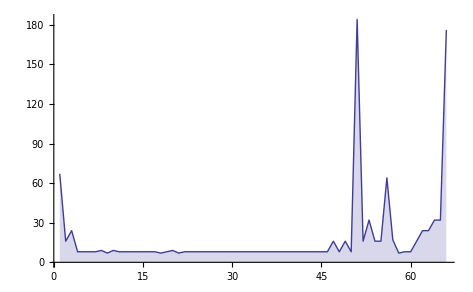
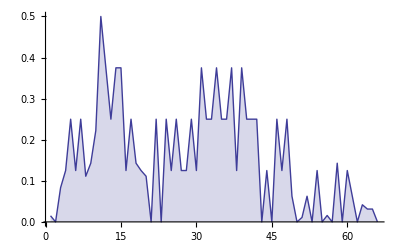
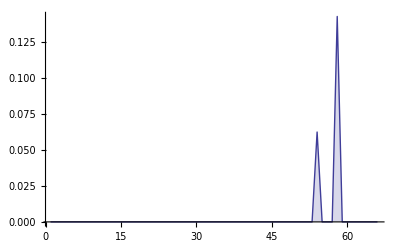

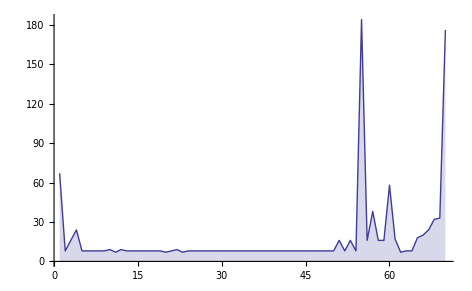
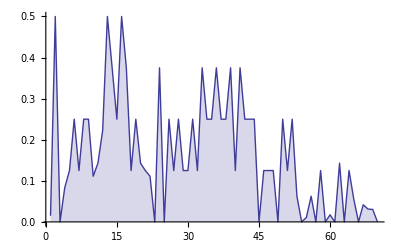
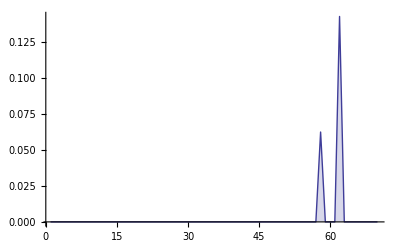

```mathematica
ShowData[A]
ShowData[B]
```